Reaching high laser intensity by a radiating electron

M. Jirka, et al, Phys. Rev. A 103, 053114
Notebook: Óscar Amaro, June 2021/Jan 2022 @ GoLP-EPP

Figure 1
Problem: what is the definition of T(τ)? By inspection it’s possible to determine an approximate relation, though it does not seem to be explicit in the text.

(47/63)^((3.01991×10^6 c^4 me^2 (ℰe/(e ES))^(2/3) α τ)/(ℰe ℏ)) ℰe

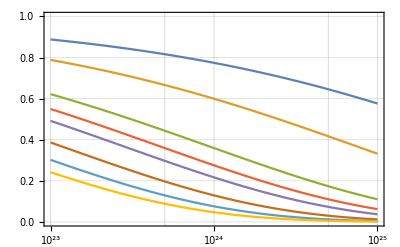

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ]

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
pc = Wγ tc;
tc=τ/(2Sqrt[2Log[2]]);
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;


ℰc=(1-16/63)^pc  ℰe (*Refine[//Simplify,{c>0,me>0,E0>0,ES>0,ℏ>0,ℰe>0,τ>0}]//FullSimplify*)


me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
T=0.67(λμm 10^-6)/c;
ES=me^2 c^3/(e ℏ);(*[V/m]*)

LogLinearPlot[{((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->0.25},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->0.5},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->50 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->30 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->2T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->50 10^9 e,τ->2T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->30 10^9 e,τ->2T,λμm->1}},{I0,10^23,10^25},PlotRange->{{10^23,10^25},{0,1}},Frame->True,GridLines->Automatic]
```

Figure 2
Confirm with figure

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,tf,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ]

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
tc=τ/(2Sqrt[2Log[2]]);
tf=τ/(Sqrt[2Log[2]]);
pc = Wγ tc;
pf = Wγ tf;
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;

me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
T=0.67(λμm 10^-6)/c;
ES=me^2 c^3/(e ℏ);(*[V/m]*)

I0=10^24;
ℰe=50 10^9 e;
τ=T;
λμm=1;

ℰc=(1-16/63)^pc  ℰe;
γec=ℰc/(me  c^2);
ℰf=(1-16/63)^pf  ℰe;

ℰc/(10^9 e)
ℰf/(10^9 e)
χec=2γec E0/ES
```

13.7695

3.79196

111.784